```mathematica
ClearAll["`*"]
Clear[Derivative]
δ = 0.7;
ω = √(34.5/67);
 r1 = DSolve[{x'[t] == v[t], v'[t] == -2δ*v[t] - ω^2*x[t], x[0] == 3, x'[0] == 2}, {x[t], v[t]}, t];
r2=DSolve[{x2'[t] == v[t], v'[t] == -2δ*v[t] - ω^2*x2[t], x2[0] == 2, x2'[0] == 3}, {x2[t], v[t]}, t];
```

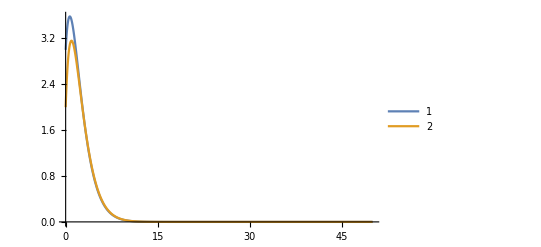

```mathematica
Plot[Evaluate[{x[t] /.r1, x2[t] /. r2}], {t, 0, 50}, PlotRange -> All, PlotLegends -> Automatic]
```